## 1d single-point evaluation (OneDfunctional.wl)

The lowest layer of the package: the 1d crossing functionals evaluated at a single point. These are the building blocks that generate1ptmx (next section) tabulates over a Δ grid. After loading, the OneDfunctional` symbols are on the context path — no qualification needed.

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "FunTable.wl"}]]
```

Arguments are (Δϕ, m, Δ): external dimension, functional order m, operator dimension Δ. The option PrecisionGoal sets the working precision (default 150). Use exact rationals. Example point: Δϕ = 0.26, m = 2, Δ = 2.

```mathematica
dphi = 3/5; m = 2; d = 2;
```

Bosonic ("minus") functionals — betaminus, alphaminus:

```mathematica
betaminus[dphi, m, d, PrecisionGoal -> 40]
```

-0.003641179786252805026194302759480855

```mathematica
alphaminus[dphi, m, d, PrecisionGoal -> 40]
```

0.005905652658761385343560337229337757

Fermionic ("plus") functionals — betaplus, alphaplus:

```mathematica
betaplus[dphi, m, d, PrecisionGoal -> 40]
```

-0.00099100571380497061035727167497604694

```mathematica
alphaplus[dphi, m, d, PrecisionGoal -> 40]
```

0.001217907111983934866074042747331587

The *funcList aggregators return all orders 0..m at once: bosonicminusfuncList and fermionicplusfuncList each give a {beta-row, alpha-row} of shape 2 × (m+1); functionalpair bundles both (shape 2 × 2 × (m+1)) — exactly the object generate1ptmx maps over the Δ grid.

```mathematica
bosonicminusfuncList[dphi, m, d, PrecisionGoal -> 40]
```

{{0,-0.114775662167351405105641093303719687,-0.003641179786252805026194302759480855},{1.66813080314115431919769352504377685,0.22149488840491787858313360874691229,0.005905652658761385343560337229337757}}

```mathematica
fermionicplusfuncList[dphi, m, d, PrecisionGoal -> 40]
```

{{-0.216150211487158854955941774946957644,-0.010900085857898723596786062796220812,-0.00099100571380497061035727167497604694},{0.988497746743322006177063442988866207,0.01274716187710925354216757034698719,0.001217907111983934866074042747331587}}

```mathematica
functionalpair[dphi, m, d, PrecisionGoal -> 40]
```

{{{0,-0.114775662167351405105641093303719687,-0.003641179786252805026194302759480855},{1.66813080314115431919769352504377685,0.22149488840491787858313360874691229,0.005905652658761385343560337229337757}},{{-0.216150211487158854955941774946957644,-0.010900085857898723596786062796220812,-0.00099100571380497061035727167497604694},{0.988497746743322006177063442988866207,0.01274716187710925354216757034698719,0.001217907111983934866074042747331587}}}

Large-Δ asymptotic counterparts (bosonicminusAsymp, fermionicplusAsymp, in OneDAsymp.wl) are used by generate1ptmx above the threshold Δ ≳ 2Δϕ + 2m + 25. Special Δϕ: 3/4 is handled in-source; 1/2 requires evaluating Δϕ at SetPrecision[dphi,200] + 10^-30.

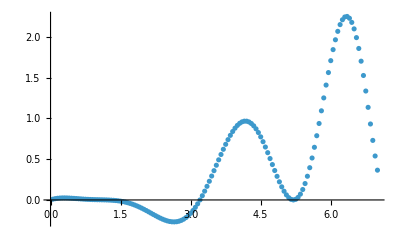

```mathematica
listbeta=betaminus[dphi,1,#,PrecisionGoal->40]&/@Range[1/20,7,1/20];
ListPlot[Transpose[{Range[1/20,7,1/20],listbeta}]]
```

## Usage example — generating a 3d functional table (.h5)

Self-contained walk-through of the generation pipeline (current API). The sections below this one are the original working scratchpad.

Load the package. Get it as a FILE so $InputFileName resolves the src/ paths:

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "FunTable.wl"}]]
```

Launch parallel kernels — the 1d generation step uses ParallelMap:

```mathematica
LaunchKernels[]
```

Choose the external dimension as an EXACT rational (avoids float rounding in the high-precision generation). Convention: dphi1d = Δϕ(3d)/2. The example is the 3d Ising point.

```mathematica
dphi3d = 5181488023/10000000000;
dphi1d = dphi3d/2;
```

Generation parameters. VeryHigh: dmaxgen=650, nmax=500 (High: 500, 350). orderMax is the functional truncation order (10 standard, 12 extended).

```mathematica
orderMax = 10; order = 10;
spinlist = Range[0, 100, 2];
dmax = 150; dmaxgen = 650; nmax = 500;
```

Step 1 — build the 1d table (.mx). The trailing True enables the exp-only normalization: the functionals are built at high precision, then rescaled by 2^(-2Δ) before conversion to machine reals to avoid 4^Δ overflow at large Δ.

```mathematica
generate1ptmx["Ising10.mx", dphi1d, orderMax, dmaxgen, True];
```

Step 2 — build the 3d functional table from the 1d .mx. "normed"->True applies the standard normalization; "fill"->30 fills the 30 grid points just below each spin's unitarity bound Δ≥ℓ+1 with the analytic continuation (ghost nodes, used only as interpolation support; "fill"->0 reproduces the classic Δ≥ℓ+1 table).

```mathematica
lp = init3DTablePatch["Ising10.mx", order, spinlist, dmax, nmax, "normed" -> True, "fill" -> 30];
```

Step 3 — export to HDF5: rename the Δtable key to dtable and drop the internal normed flag (the LP loader's schema).

```mathematica
lpNew = KeyDrop[KeyMap[# /. "Δtable" -> "dtable" &, lp], "normed"];
Export["Ising10.h5", Normal[lpNew], "HDF5"];
```

Notes. (1) 1d dphi = 3d Δϕ / 2. (2) Grids: 1d Range[0, dmaxgen, 1/202]; 2d/3d spacing 1/101 (halfstep = 101), index i ⟷ Δ = (i-1)/101. (3) Packed table dims {nspins, nΔ, funcnum}; each row is Δ=0 (spin 0 only), zero for 0<Δ<ℓ+1-fill/101, populated above. (4) Special dphi: 3d Δϕ=3/2 (1d 3/4) is handled in-source; 3d Δϕ=1 (1d 1/2) requires evaluating dphi at SetPrecision[dphi,200]+10^-30.